## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet",}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet}

### Sigma

```mathematica
fitVar = "PDrive_sigmaSI90_z"
```

PDrive_sigmaSI90_z

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

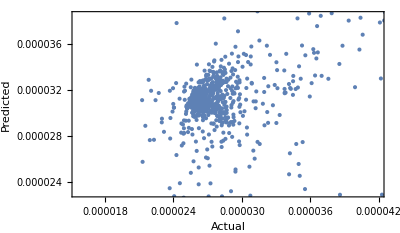

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 1.82218×10^-10 | 1.82218×10^-10 | 1.00801 | 0.315662
L1PhaseSet | 1 | 1.38866×10^-9 | 1.38866×10^-9 | 7.6819 | 0.00569764
L2PhaseSet | 1 | 5.35758×10^-8 | 5.35758×10^-8 | 296.374 | 2.48901×10^-57
L3PhaseSet | 1 | 1.76242×10^-9 | 1.76242×10^-9 | 9.74946 | 0.00185348
Error | 864 | 1.56186×10^-7 | 1.80771×10^-10 |  | 
Total | 868 | 2.13095×10^-7 |  |  |

```mathematica
lmSigma = lm;
```

### Spacing

```mathematica
fitVar = "bunchSpacing"
```

bunchSpacing

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

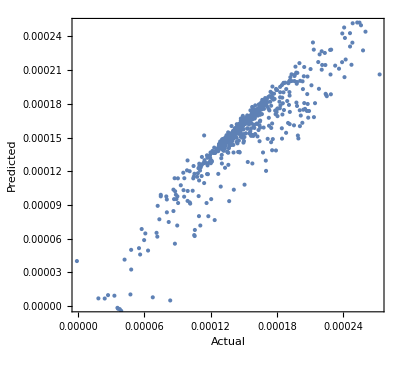

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

General::munfl: Exp[-855.978] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 1.73104×10^-8 | 1.73104×10^-8 | 22.5196 | 2.43349×10^-6
L1PhaseSet | 1 | 1.77832×10^-6 | 1.77832×10^-6 | 2313.47 | 1.50294×10^-246
L2PhaseSet | 1 | 4.11373×10^-6 | 4.11373×10^-6 | 5351.66 | 0.
L3PhaseSet | 1 | 1.48601×10^-8 | 1.48601×10^-8 | 19.3319 | 0.000012354
Error | 864 | 6.64142×10^-7 | 7.68682×10^-10 |  | 
Total | 868 | 6.58837×10^-6 |  |  |

```mathematica
lmSpacing = lm;
```

## Solve

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["BestFit"]
```

-0.000276133+0.0000130223 L0BPhaseSet+0.0000543178 L1PhaseSet-0.0000400835 L2PhaseSet+5.71058×10^-6 L3PhaseSet

```mathematica
allowedDeltaFromNominal = 5;
sol = NMinimize[{
lmSigma["BestFit"],
lmSpacing["BestFit"] >140*^-6 &&
lmSpacing["BestFit"] <160*^-6 && 
L0BPhaseSet>-allowedDeltaFromNominal&& 
L0BPhaseSet<allowedDeltaFromNominal&& 
L3PhaseSet>-allowedDeltaFromNominal&& 
L3PhaseSet<allowedDeltaFromNominal&& 
L1PhaseSet>(-20-allowedDeltaFromNominal)&& 
L1PhaseSet<(-20+allowedDeltaFromNominal)&& 
L2PhaseSet>(-40-allowedDeltaFromNominal)&& 
L2PhaseSet<(-40+allowedDeltaFromNominal)
},
{L0BPhaseSet, L1PhaseSet, L2PhaseSet, L3PhaseSet}
]
```

{1.35677×10^-6,{L0BPhaseSet→-5.,L1PhaseSet→-16.4426,L2PhaseSet→-35.,L3PhaseSet→-5.}}

```mathematica
lmSigma["BestFit"]/.sol[[2]]
```

1.35677×10^-6

Closest point in the dataset

```mathematica
MinimalBy[
raw,
(#L0BPhaseSet -(L0BPhaseSet&/@sol[[2]]) )^2+(#L1PhaseSet -(L1PhaseSet&/@sol[[2]]) )^2+(#L2PhaseSet -(L2PhaseSet&/@sol[[2]]) )^2+(#L3PhaseSet -(L3PhaseSet&/@sol[[2]]) )^2&
]
```

{<|L0BPhaseSet→2.05946,L1PhaseSet→-24.1676,L2PhaseSet→-37.5943,L3PhaseSet→-0.623337,S1EL_xOffset→0.00210144,S1EL_yOffset→-0.00032704,S2EL_xOffset→-0.00203904,S2EL_yOffset→-0.0000823816,S2ER_xOffset→-0.00130543,S2ER_yOffset→-0.000280678,S1ER_xOffset→0.000289756,S1ER_yOffset→-0.000434121,XC1FFkG→0.0391485,XC3FFkG→-0.0176064,YC1FFkG→-0.00462573,YC2FFkG→0.0391169,PDrive_mean_x→0.0000965848,PDrive_mean_y→-1.3429×10^-6,PDrive_sigma_x→0.0000693326,PDrive_sigma_y→0.0000309348,PDrive_mean_xp→-0.0000443809,PDrive_mean_yp→0.000131836,PDrive_median_x→0.000117767,PDrive_median_y→-5.5457×10^-6,PDrive_median_xp→0.0000448954,PDrive_median_yp→0.00013921,PDrive_sigmaSI90_x→0.0000606721,PDrive_sigmaSI90_y→0.0000272476,PDrive_sigmaSI90_z→0.0000260489,PDrive_emitSI90_x→0.000232662,PDrive_emitSI90_y→0.0000119867,PDrive_zCentroid→991.332,PWitness_mean_x→0.000113249,PWitness_mean_y→0.0000327753,PWitness_sigma_x→0.0000270407,PWitness_sigma_y→0.0000335589,PWitness_mean_xp→-0.000402143,PWitness_mean_yp→0.000163605,PWitness_median_x→0.000108996,PWitness_median_y→0.0000353986,PWitness_median_xp→-0.000559185,PWitness_median_yp→0.000169805,PWitness_sigmaSI90_x→0.0000259463,PWitness_sigmaSI90_y→0.0000305165,PWitness_sigmaSI90_z→0.0000569734,PWitness_emitSI90_x→0.000129371,PWitness_emitSI90_y→0.0000115629,PWitness_zCentroid→991.332,bunchSpacing→0.0000250402,transverseCentroidOffset→0.0000379704,lostChargeFraction→0.,errorTerm_lostChargeFraction→0.,errorTerm_bunchSpacing→132158.,errorTerm_transverseOffset→6.11402×10^6,errorTerm_angleOffset→0.,errorTerm_mainObjective→1.23685,maximizeMe→9.606×10^-7|>}